```mathematica
a=2x+3y==0
```

2 x+3 y==0

```mathematica
b=Solve[a,y]
```

{{y→-(2 x)/3}}

```mathematica
b[[1,1,2]]
```

```mathematica
-(2 x)/□
```

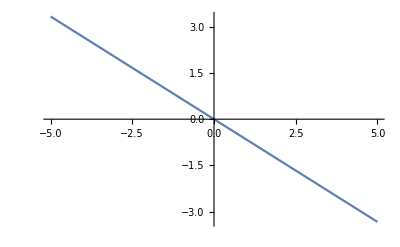

```mathematica
img1=Plot[b[[1,1,2]],{x,-5,5}]
```

```mathematica
a2=x-y==2
```

x-y==2

```mathematica
b2=Solve[a2,y]
```

{{y→-2+x}}

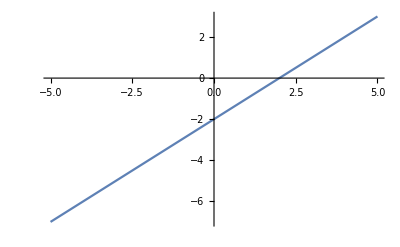

```mathematica
img2=Plot[b2[[1,1,2]],{x,-5,5}]
```

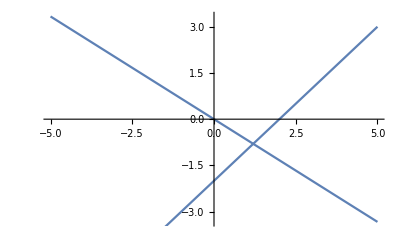

```mathematica
Show[img1,img2]
```

```mathematica
Graficar[ec1_,ec2_]:=Block[{a1,a2,b1,b2,img1,img2},
a1=Solve[ec1,y];
a2=Solve[ec2,y];
img1=Plot[a1[[1,1,2]],{x,-10,10}];
img2=Plot[a2[[1,1,2]],{x,-10,10}];
Print[a1[[1,1,2]]]
Show[img1,img2]

]
```

```mathematica
Graficar[2x+3y==0,x-y==2]
```

-(2 x)/3

Null -Graphics-

```mathematica
A={1,2,3,l,p,m}
```

{1,2,3,l,p,m}

```mathematica
Length[A]
```

6

```mathematica
Insert[A,{1,2,3},-1]
```

```mathematica
{1,2,3,l,p,m,{1,2,3}}
```

```mathematica
Insert[A,{1,2,3},3]
```

{1,2,{1,2,3},3,l,p,m}

```mathematica
Flatten[Append[A,{1,2,3}]]
```

{1,2,3,l,p,m,1,2,3}

```mathematica
DeleteCases[A,2]
```

{1,3,l,p,m}